# Lattice Models

## 4-Qubit gas model with one qubit temperature variation Import::nffil: File \"\</Users/uja5020/Desktop//DensityMatrixTools.wl\>\" not found during Import.

```mathematica
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4]};
vals = RandomSample[Table[i,{i,4}]];
Association[Table[items[[i]]-> vals[[i]],{i,4}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,4];
Hi1 = SubsysInteraction;
interactionUnitary =  SparseArray[MatrixExp[I (Hi1) .1]]
]
```

```mathematica
ρi = NThermalQBit[{.2,.4,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO = RandomOrder[];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,500}];
```

```mathematica
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
```

```mathematica
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
```

```mathematica
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
```

```mathematica
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
```

Part::partw: Part 501 of {{0.158183,0.000185235,0.156946,0.158249},{0.158073,0.00015991,0.15807,0.153573},{0.153334,0.0000650912,0.154069,0.145564},{0.140288,3.81416×10^-6,0.146,0.133614},{0.153762,0.0000774229,0.154748,0.147039},{0.144416,8.95218×10^-7,0.148588,0.136032},«40»,{0.119473,0.00355932,0.0671736,0.114878},{0.116922,0.00548727,0.0534862,0.11674},{0.114392,0.00799437,0.0456805,0.110898},{0.11729,0.00517993,0.0574103,0.112375},«450»} does not exist.

```mathematica
ChangeinExtractablework[[2]]
```

If[{0.0012294,0.0000267392,0.0026637,0.0000107401}>0,ExtractableWorkOverTime⟦i+1⟧-ExtractableWorkOverTime⟦i⟧,0]

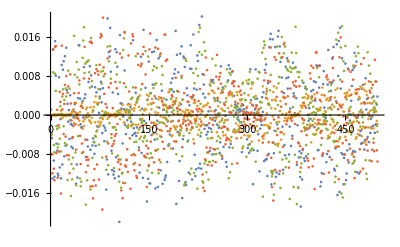

```mathematica
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]
```

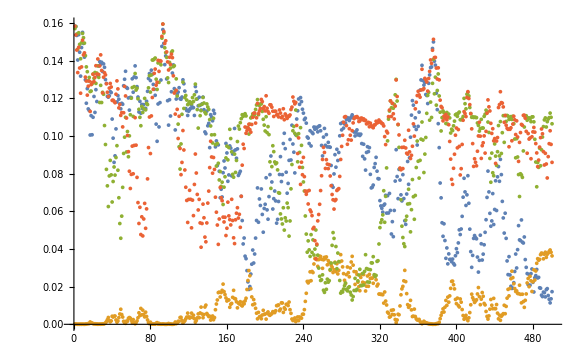

```mathematica
ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic,PlotRange->All]
```

```mathematica
ChangeinExtractablework//MatrixPlot
```

-Graphics-

```mathematica
Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

-Graphics-

## 8-Qubit gas model with one qubit temperature variation

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5],Subscript[𝒬, 6],Subscript[𝒬, 7],Subscript[𝒬, 8]};
vals = RandomSample[Table[i,{i,8}]];
Association[Table[items[[i]]-> vals[[i]],{i,8}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,4];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^4]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2) .1]]
]
```

```mathematica
ρi = NThermalQBit[{.2,.2,.2,.2,.4,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO = RandomOrder[];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,500}];
```

```mathematica
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
```

```mathematica
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
```

```mathematica
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
```

```mathematica
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
```

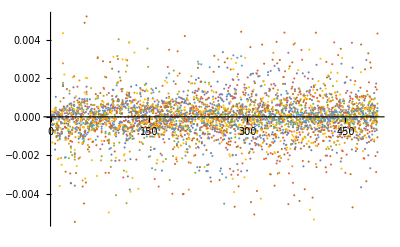

```mathematica
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]
```

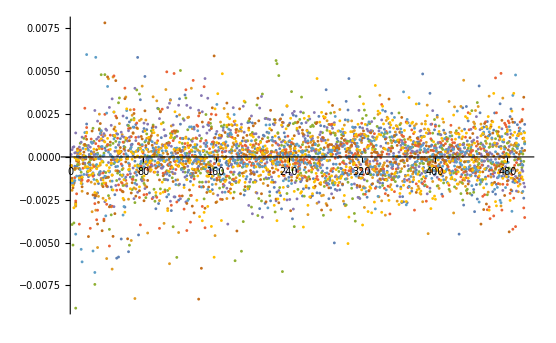

```mathematica
500 trials
```

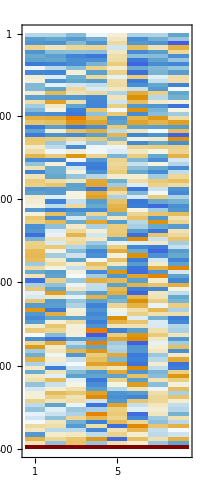

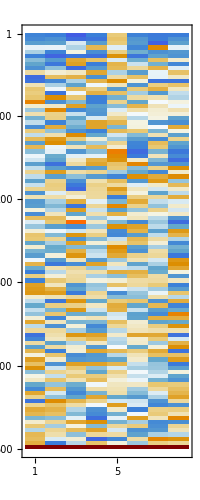

```mathematica
ChangeinExtractablework//MatrixPlot
```

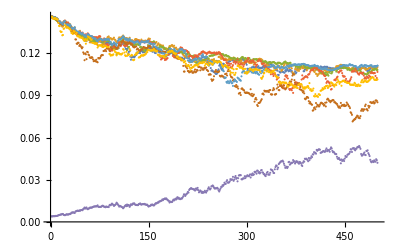

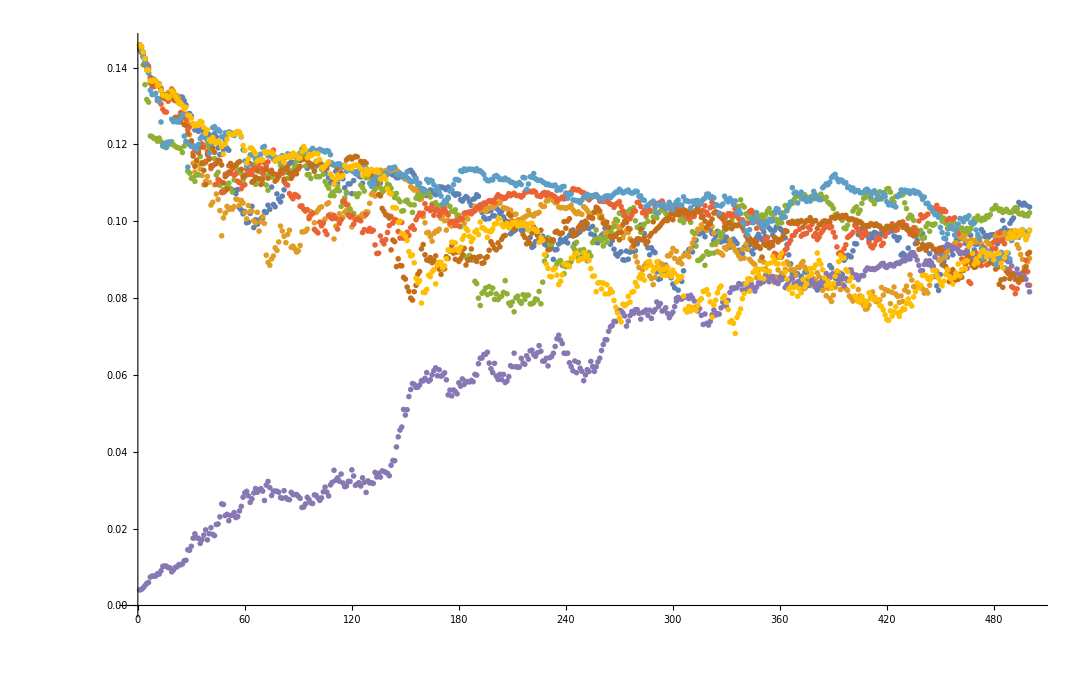

```mathematica
ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]
```

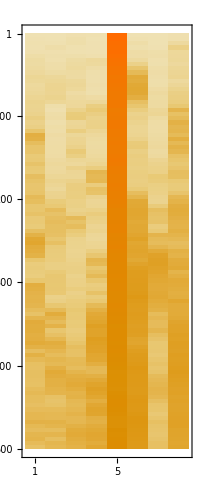

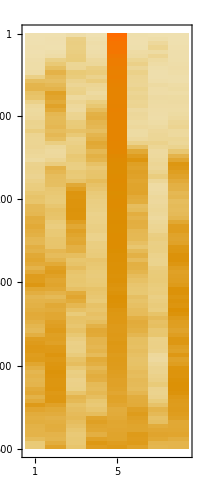

```mathematica
Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

## 8-Qubit gas model with multiple qubit temperature variation

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5],Subscript[𝒬, 6],Subscript[𝒬, 7],Subscript[𝒬, 8]};
vals = RandomSample[Table[i,{i,8}]];
Association[Table[items[[i]]-> vals[[i]],{i,8}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,interactionUnitary},
SubsysInteraction = RandomHamiltonian[2,4];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^4]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2) .1]]
]
```

```mathematica
ρi = NThermalQBit[{.2,.4,.2,.2,.4,.2,.4,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO = RandomOrder[];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,500}];
```

```mathematica
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
```

```mathematica
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
```

```mathematica
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
```

```mathematica
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
```

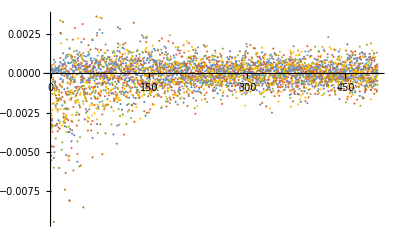

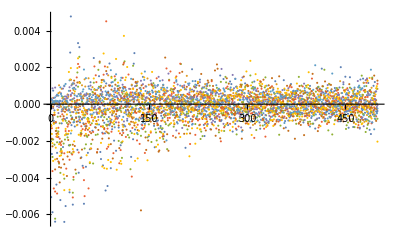

```mathematica
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]
```

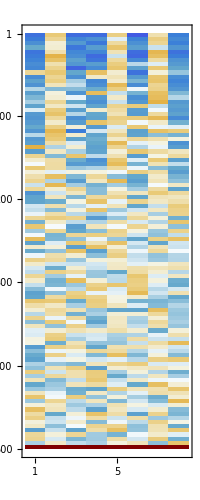

```mathematica
ChangeinExtractablework//MatrixPlot
```

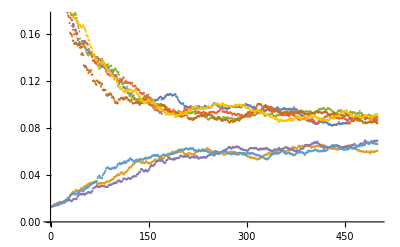

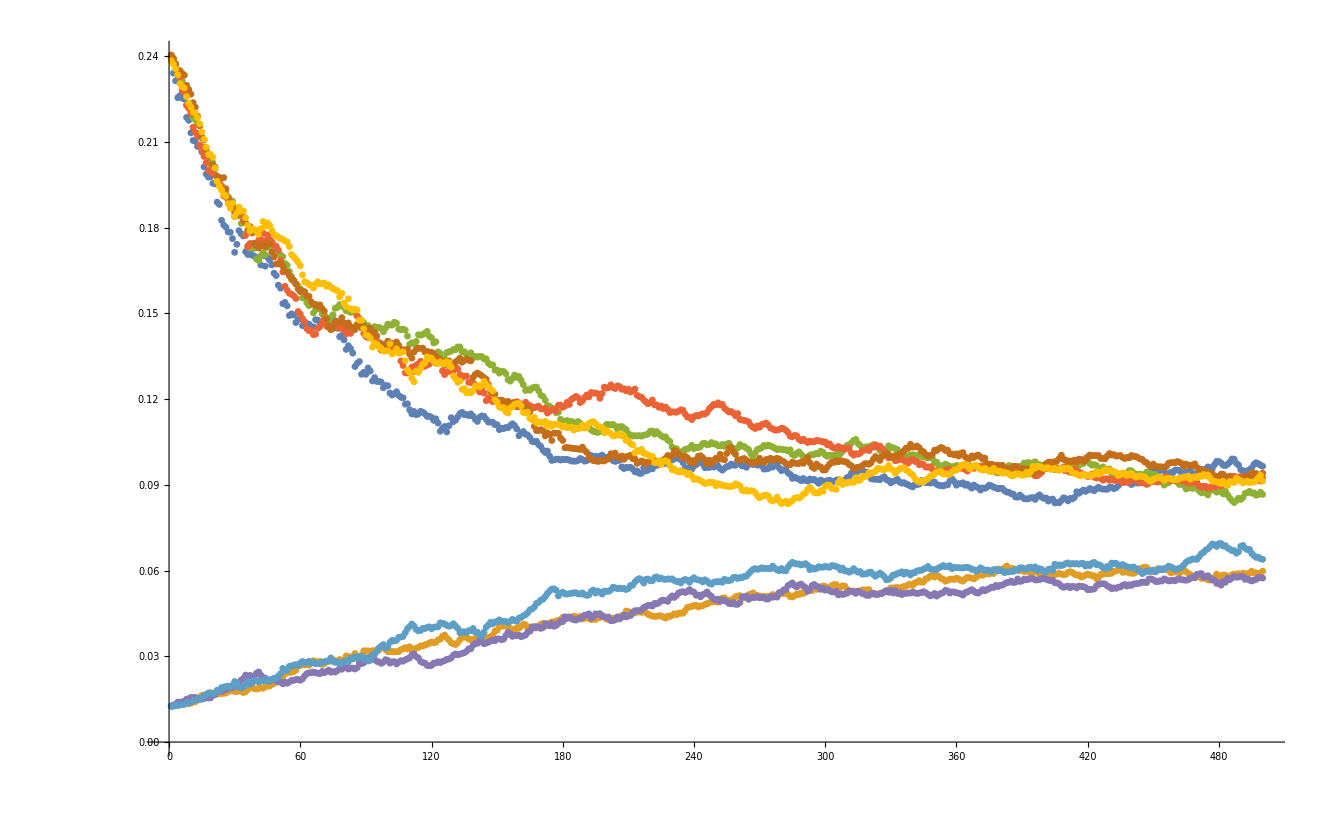

```mathematica
ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]
```

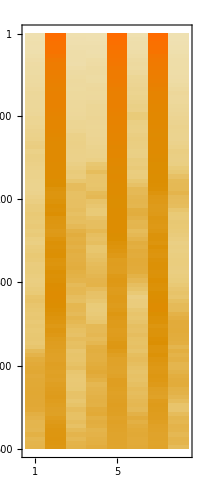

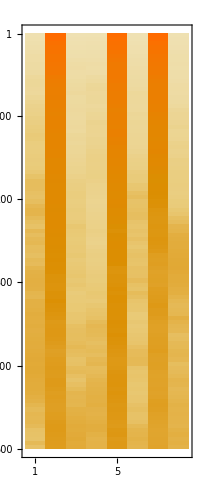

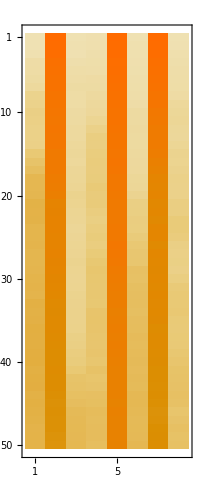

```mathematica
Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

## 8-qubits in a line with two qubit nearest neighbour interaction

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,2];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^6]];
Hi2= KroneckerProduct[IdentityMatrix[2^2],SubsysInteraction,IdentityMatrix[2^4]];
Hi3=KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction,IdentityMatrix[2^2]];
Hi4=KroneckerProduct[IdentityMatrix[2^6],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2+Hi3+Hi4) .1]]
]
```

```mathematica
PossibleOrders = {
<|Subscript[𝒬, 1]->1,Subscript[𝒬, 2]->2,Subscript[𝒬, 3]->3,Subscript[𝒬, 4]->4,Subscript[𝒬, 5]->5,Subscript[𝒬, 6]->6,Subscript[𝒬, 7]->7,Subscript[𝒬, 8]->8|>,
<|Subscript[𝒬, 1]-> 8,Subscript[𝒬, 2]-> 1,Subscript[𝒬, 3]-> 2,Subscript[𝒬, 4]-> 3,Subscript[𝒬, 5]-> 4,Subscript[𝒬, 6]-> 5,Subscript[𝒬, 7]-> 6,Subscript[𝒬, 8]-> 7|>
};
```

```mathematica
ρi = NThermalQBit[{.2,.2,.2,.2,.4,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO  =RandomChoice[PossibleOrders];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,500}];
```

```mathematica
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
```

```mathematica
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
```

```mathematica
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
```

```mathematica
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
```

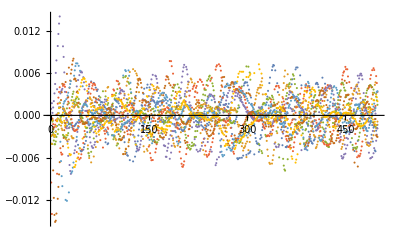

```mathematica
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]
```

#### 500 trials

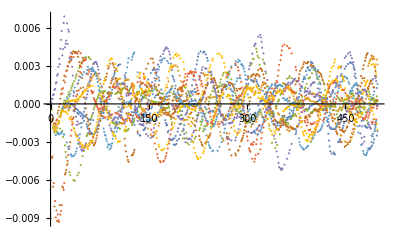

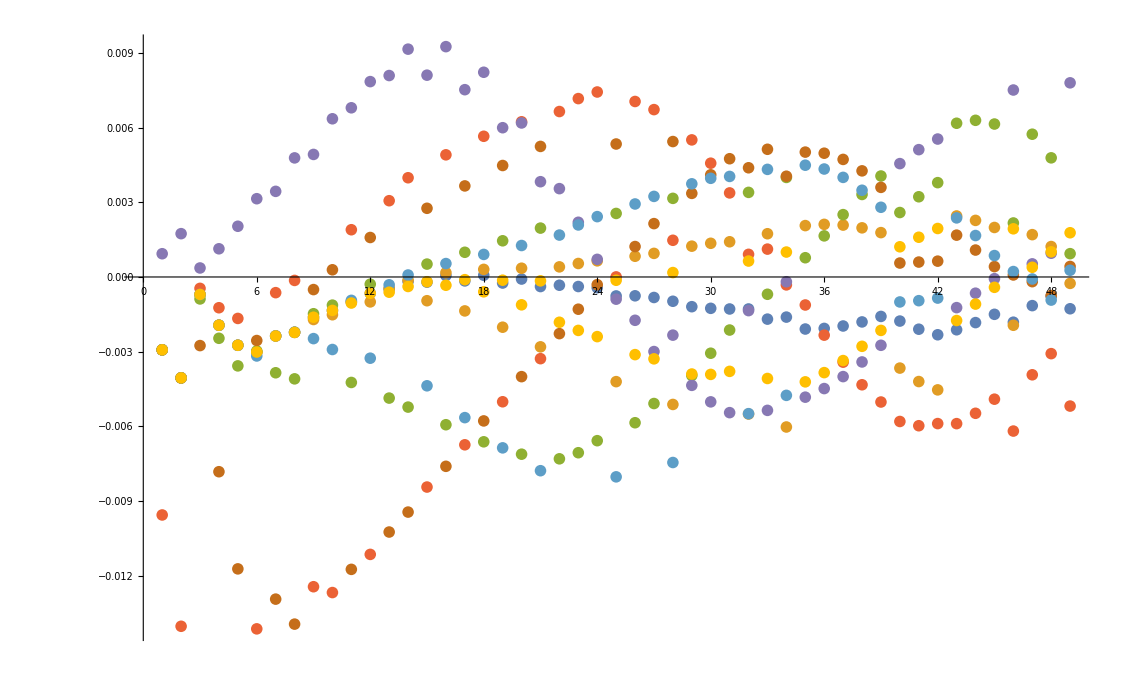

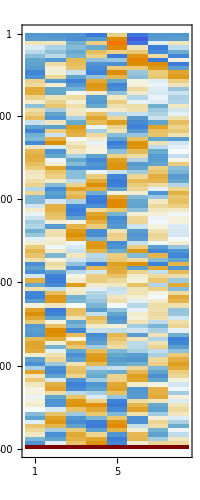

```mathematica
ChangeinExtractablework//MatrixPlot
```

#### 500 trials

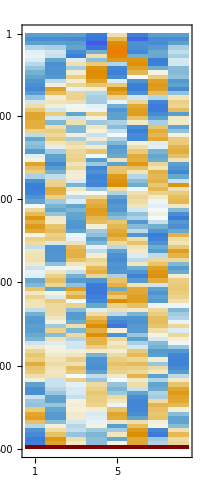

-Graphics-

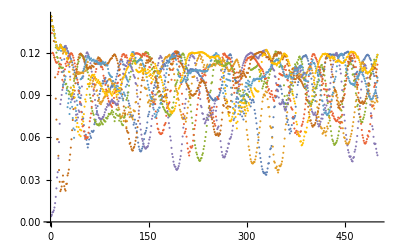

```mathematica
ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]
```

#### 500 trials

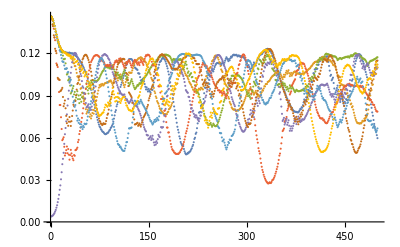

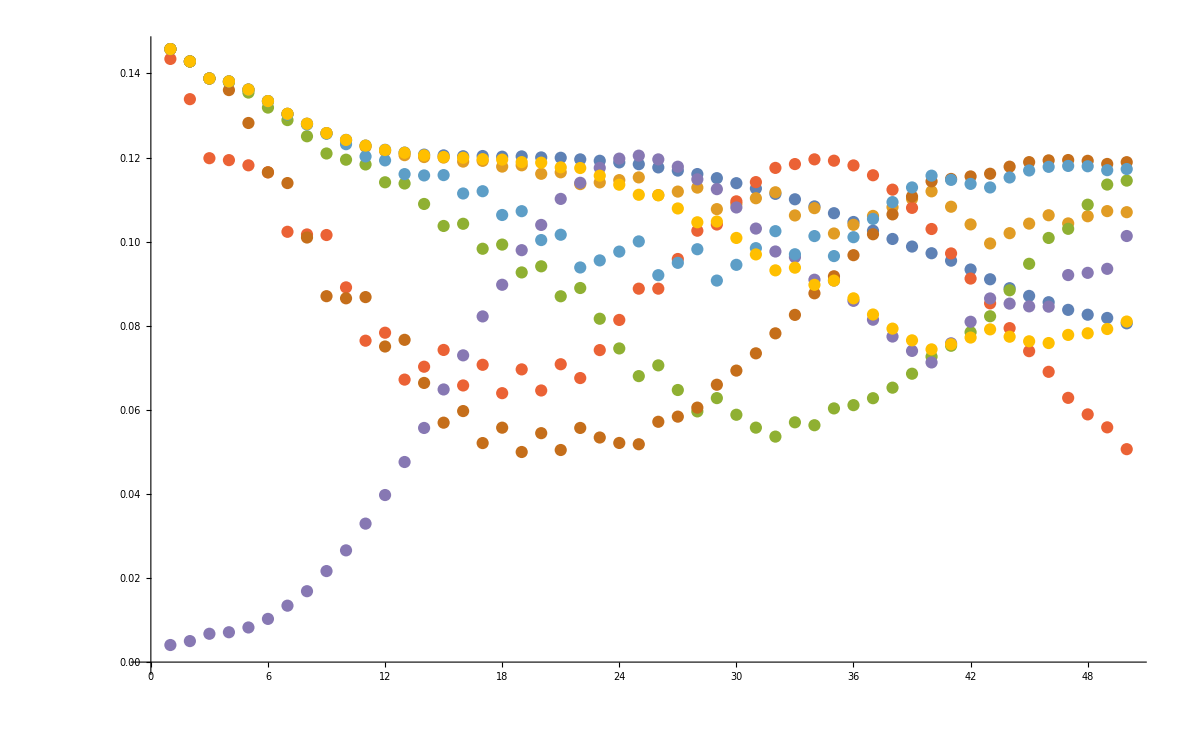

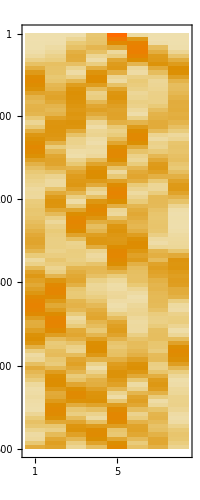

```mathematica
Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

#### 500 trials

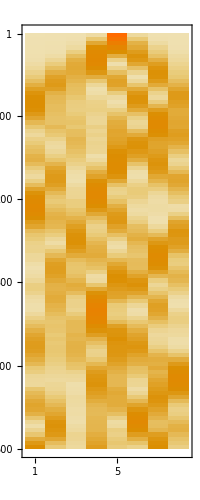

-Graphics-

## 8-qubits in a line with two qubit nearest neighbour interaction (multiple temp variation)

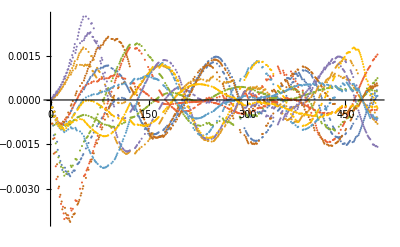

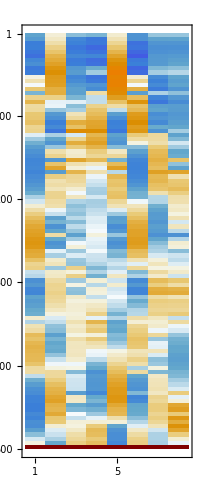

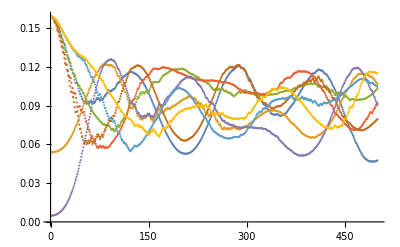

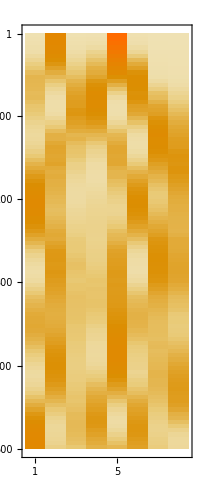

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,2];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^6]];
Hi2= KroneckerProduct[IdentityMatrix[2^2],SubsysInteraction,IdentityMatrix[2^4]];
Hi3=KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction,IdentityMatrix[2^2]];
Hi4=KroneckerProduct[IdentityMatrix[2^6],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2+Hi3+Hi4) .1]]
]
PossibleOrders = {
<|Subscript[𝒬, 1]->1,Subscript[𝒬, 2]->2,Subscript[𝒬, 3]->3,Subscript[𝒬, 4]->4,Subscript[𝒬, 5]->5,Subscript[𝒬, 6]->6,Subscript[𝒬, 7]->7,Subscript[𝒬, 8]->8|>,
<|Subscript[𝒬, 1]-> 8,Subscript[𝒬, 2]-> 1,Subscript[𝒬, 3]-> 2,Subscript[𝒬, 4]-> 3,Subscript[𝒬, 5]-> 4,Subscript[𝒬, 6]-> 5,Subscript[𝒬, 7]-> 6,Subscript[𝒬, 8]-> 7|>
};
ρi = NThermalQBit[{.2,.3,.2,.2,.4,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO  =RandomChoice[PossibleOrders];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,500}];
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];

ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]



ChangeinExtractablework//MatrixPlot



ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]



Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

#### 500 trials

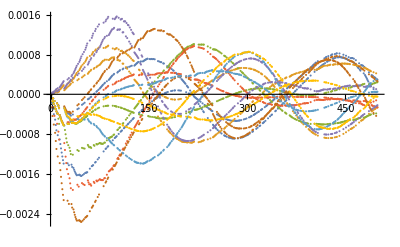

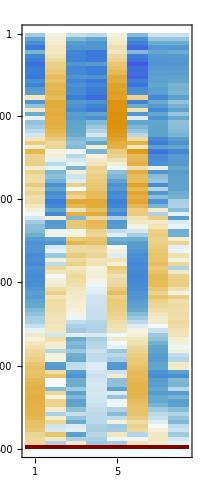

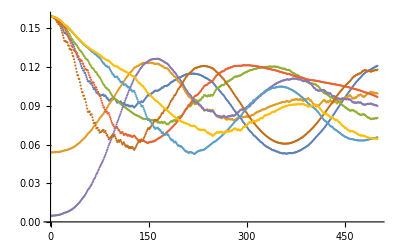

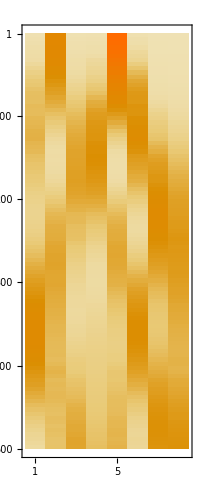

```mathematica
8-Qubits on a lattice
```

## Unitary translationally invariant (same everywhere at every time step)

### Four qubit pockets (single temp variation)

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5],Subscript[𝒬, 6],Subscript[𝒬, 7],Subscript[𝒬, 8]};
vals = RandomSample[Table[i,{i,8}]];
Association[Table[items[[i]]-> vals[[i]],{i,8}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,4];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^4]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2) .1]]
]
```

```mathematica
PossibleOrders = {
<|Subscript[𝒬, 1]->1,Subscript[𝒬, 2]->2,Subscript[𝒬, 3]->3,Subscript[𝒬, 4]->4,Subscript[𝒬, 5]->5,Subscript[𝒬, 6]->6,Subscript[𝒬, 7]->7,Subscript[𝒬, 8]->8|>,
<|Subscript[𝒬, 1]-> 5,Subscript[𝒬, 2]-> 6,Subscript[𝒬, 3]-> 3,Subscript[𝒬, 4]-> 4,Subscript[𝒬, 5]-> 1,Subscript[𝒬, 6]-> 2,Subscript[𝒬, 7]-> 7,Subscript[𝒬, 8]-> 8|>
};
```

```mathematica
ρi = NThermalQBit[{.2,.2,.2,.2,.5,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
(*RO = RandomOrder[];*)
RO  =RandomChoice[PossibleOrders];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,500}];
```

```mathematica
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
```

```mathematica
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
```

```mathematica
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
```

```mathematica
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
```

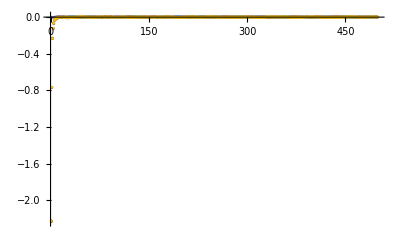

```mathematica
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]
```

#### 500 trials

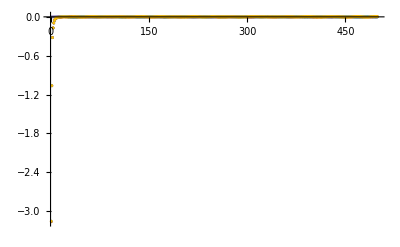

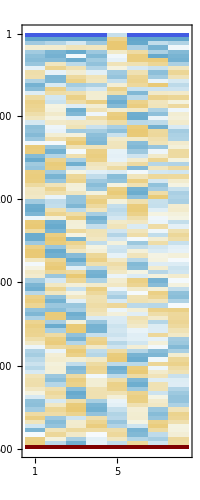

```mathematica
ChangeinExtractablework//MatrixPlot
```

#### 500 trials

-Graphics-

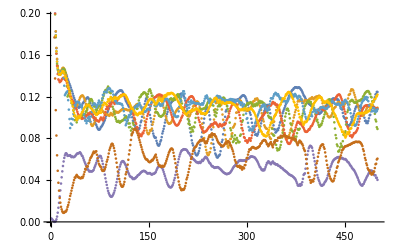

```mathematica
ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]
```

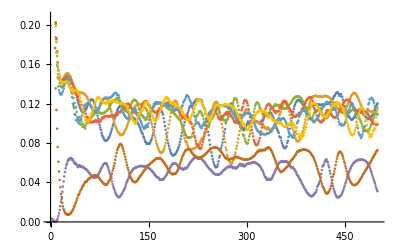

```mathematica
500 trials
```

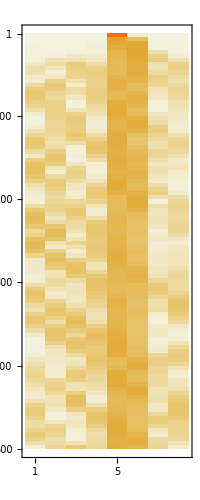

```mathematica
Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

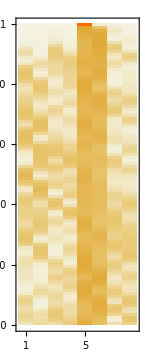

```mathematica
500 trials
```

### Four qubit pockets (multiple temp variation)

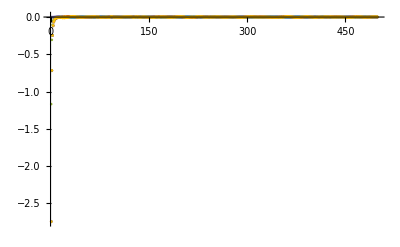

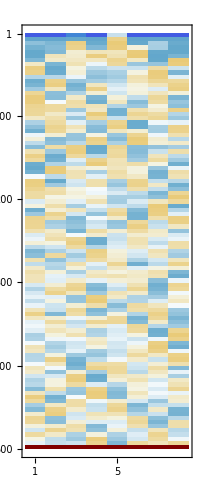

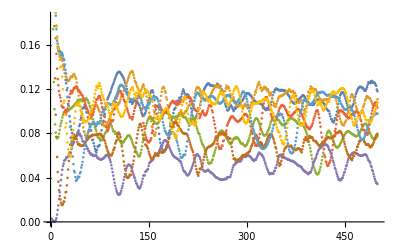

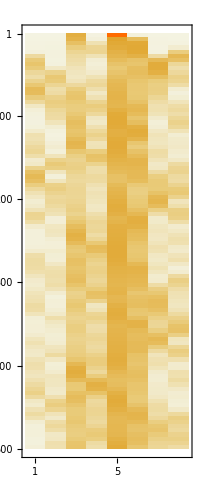

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5],Subscript[𝒬, 6],Subscript[𝒬, 7],Subscript[𝒬, 8]};
vals = RandomSample[Table[i,{i,8}]];
Association[Table[items[[i]]-> vals[[i]],{i,8}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,4];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^4]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2) .1]]
]
PossibleOrders = {
<|Subscript[𝒬, 1]->1,Subscript[𝒬, 2]->2,Subscript[𝒬, 3]->3,Subscript[𝒬, 4]->4,Subscript[𝒬, 5]->5,Subscript[𝒬, 6]->6,Subscript[𝒬, 7]->7,Subscript[𝒬, 8]->8|>,
<|Subscript[𝒬, 1]-> 5,Subscript[𝒬, 2]-> 6,Subscript[𝒬, 3]-> 3,Subscript[𝒬, 4]-> 4,Subscript[𝒬, 5]-> 1,Subscript[𝒬, 6]-> 2,Subscript[𝒬, 7]-> 7,Subscript[𝒬, 8]-> 8|>
};
ρi = NThermalQBit[{.2,.2,.3,.2,.5,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
(*RO = RandomOrder[];*)
RO  =RandomChoice[PossibleOrders];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,500}];
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]

ChangeinExtractablework//MatrixPlot

ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]

Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

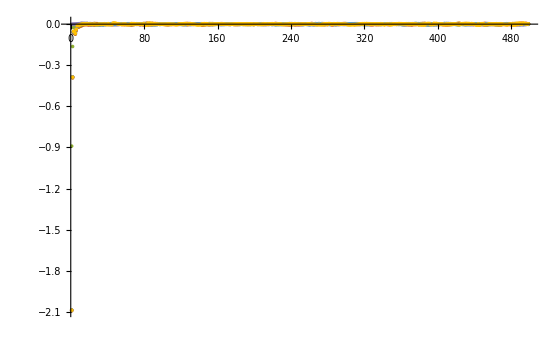

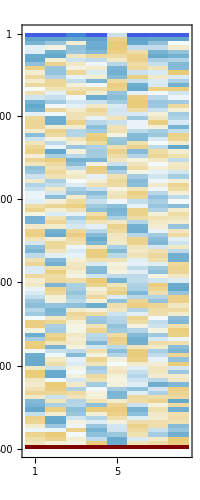

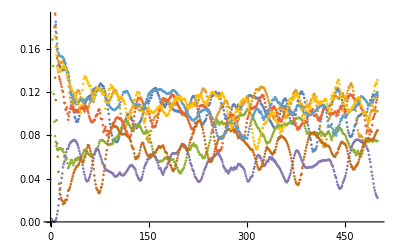

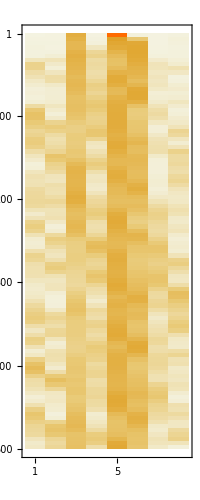

```mathematica
500 trials
```

## Random Unitary (different unitaries in each pocket at every time step)

### Four qubit pockets (single temp variation)

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,SubsysInteraction1,SubsysInteraction2,ExtractableWorkOverTime,ChangeinExtractablework]
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5],Subscript[𝒬, 6],Subscript[𝒬, 7],Subscript[𝒬, 8]};
vals = RandomSample[Table[i,{i,8}]];
Association[Table[items[[i]]-> vals[[i]],{i,8}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,interactionUnitary},
SubsysInteraction1 = RandomHamiltonian[1,4];
SubsysInteraction2 = RandomHamiltonian[3,4];
Hi1 = KroneckerProduct[SubsysInteraction1,IdentityMatrix[2^4]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction2];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2) .1]]
]
```

```mathematica
PossibleOrders = {
<|Subscript[𝒬, 1]->1,Subscript[𝒬, 2]->2,Subscript[𝒬, 3]->3,Subscript[𝒬, 4]->4,Subscript[𝒬, 5]->5,Subscript[𝒬, 6]->6,Subscript[𝒬, 7]->7,Subscript[𝒬, 8]->8|>,
<|Subscript[𝒬, 1]-> 5,Subscript[𝒬, 2]-> 6,Subscript[𝒬, 3]-> 3,Subscript[𝒬, 4]-> 4,Subscript[𝒬, 5]-> 1,Subscript[𝒬, 6]-> 2,Subscript[𝒬, 7]-> 7,Subscript[𝒬, 8]-> 8|>
};
```

```mathematica
ρi = NThermalQBit[{.2,.2,.2,.2,.5,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
(*RO = RandomOrder[];*)
RO  =RandomChoice[PossibleOrders];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,500}];
```

```mathematica
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
```

```mathematica
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
```

```mathematica
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
```

```mathematica
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
```

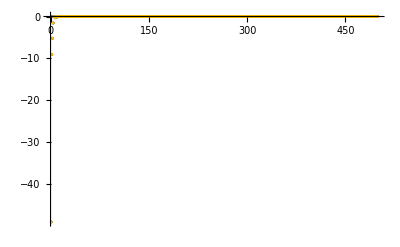

```mathematica
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]
```

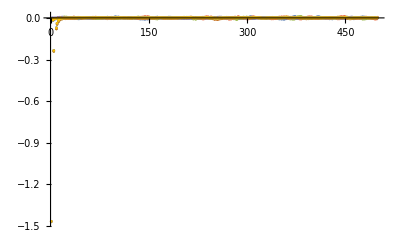

```mathematica
500 trials
```

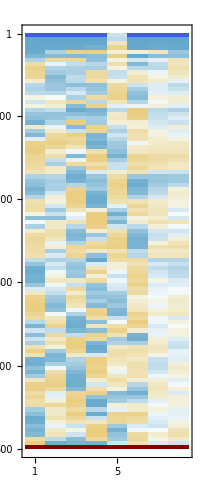

```mathematica
ChangeinExtractablework//MatrixPlot
```

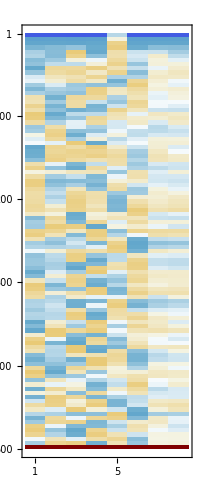

```mathematica
500 trials
```

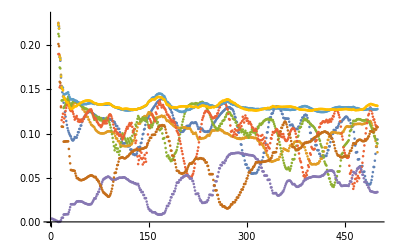

```mathematica
ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]
```

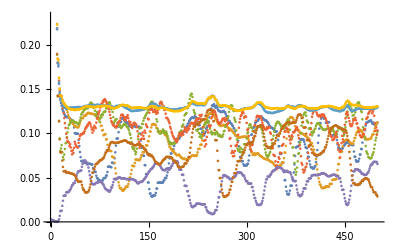

```mathematica
500 trials
```

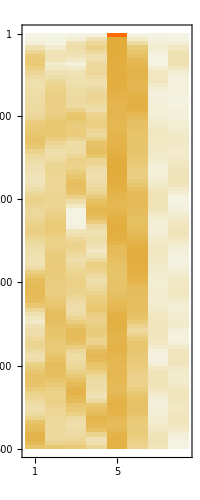

```mathematica
Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

```mathematica
500 trials
```

-Graphics-

### Four qubit pockets (multiple temp variation)

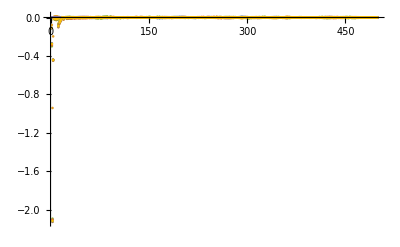

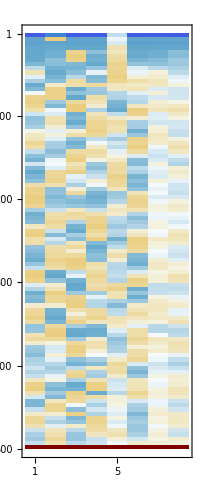

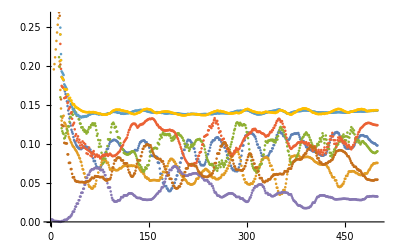

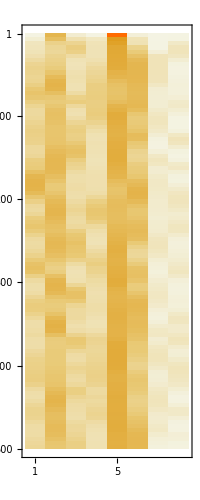

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary,RandomUnitary,PossibleOrders,SubsysInteraction1,SubsysInteraction2,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5],Subscript[𝒬, 6],Subscript[𝒬, 7],Subscript[𝒬, 8]};
vals = RandomSample[Table[i,{i,8}]];
Association[Table[items[[i]]-> vals[[i]],{i,8}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,interactionUnitary},
SubsysInteraction1 = RandomHamiltonian[1,4];
SubsysInteraction2 = RandomHamiltonian[3,4];
Hi1 = KroneckerProduct[SubsysInteraction1,IdentityMatrix[2^4]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction2];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2) .1]]
]
PossibleOrders = {
<|Subscript[𝒬, 1]->1,Subscript[𝒬, 2]->2,Subscript[𝒬, 3]->3,Subscript[𝒬, 4]->4,Subscript[𝒬, 5]->5,Subscript[𝒬, 6]->6,Subscript[𝒬, 7]->7,Subscript[𝒬, 8]->8|>,
<|Subscript[𝒬, 1]-> 5,Subscript[𝒬, 2]-> 6,Subscript[𝒬, 3]-> 3,Subscript[𝒬, 4]-> 4,Subscript[𝒬, 5]-> 1,Subscript[𝒬, 6]-> 2,Subscript[𝒬, 7]-> 7,Subscript[𝒬, 8]-> 8|>
};
ρi = NThermalQBit[{.2,.3,.2,.2,.5,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
(*RO = RandomOrder[];*)
RO  =RandomChoice[PossibleOrders];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,500}];
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]

ChangeinExtractablework//MatrixPlot

ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]

Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

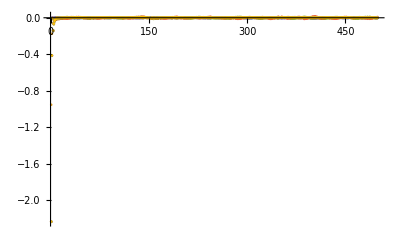

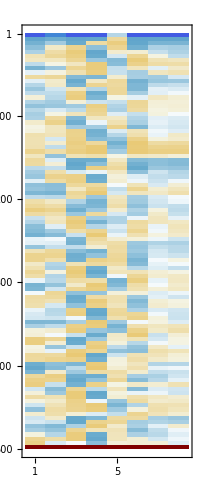

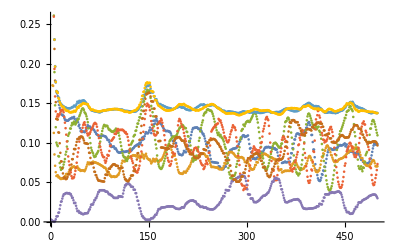

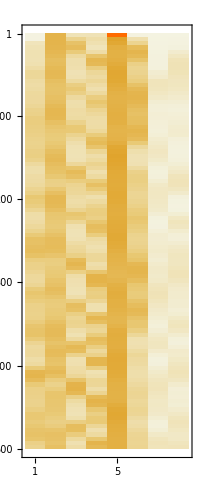

```mathematica
500 trials
```

## 12-Qubit gas model with one qubit temperature variation

```mathematica
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5],Subscript[𝒬, 6],Subscript[𝒬, 7],Subscript[𝒬, 8],Subscript[𝒬, 9],Subscript[𝒬, 10],Subscript[𝒬, 11],Subscript[𝒬, 12]};
vals = RandomSample[Table[i,{i,12}]];
Association[Table[items[[i]]-> vals[[i]],{i,12}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,Hi3,interactionUnitary},
SubsysInteraction = RandomHamiltonian[2,4];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^8]];
Hi2= KroneckerProduct[IdentityMatrix[2^8],SubsysInteraction];
Hi3= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction,IdentityMatrix[2^4]];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2+Hi3) .1]]
]
Print[RandomUnitary]
```

SparseArray[<97336>, {4096, 4096}]

```mathematica
c\0
```

```mathematica
ρi = NThermalQBit[{.2,.2,.2,.2,.2,.2,.4,.2,.2,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO = RandomOrder[];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,10}];
```

```mathematica
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]],
{Ρ,DMS}];
```

```mathematica
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
```

```mathematica
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
```

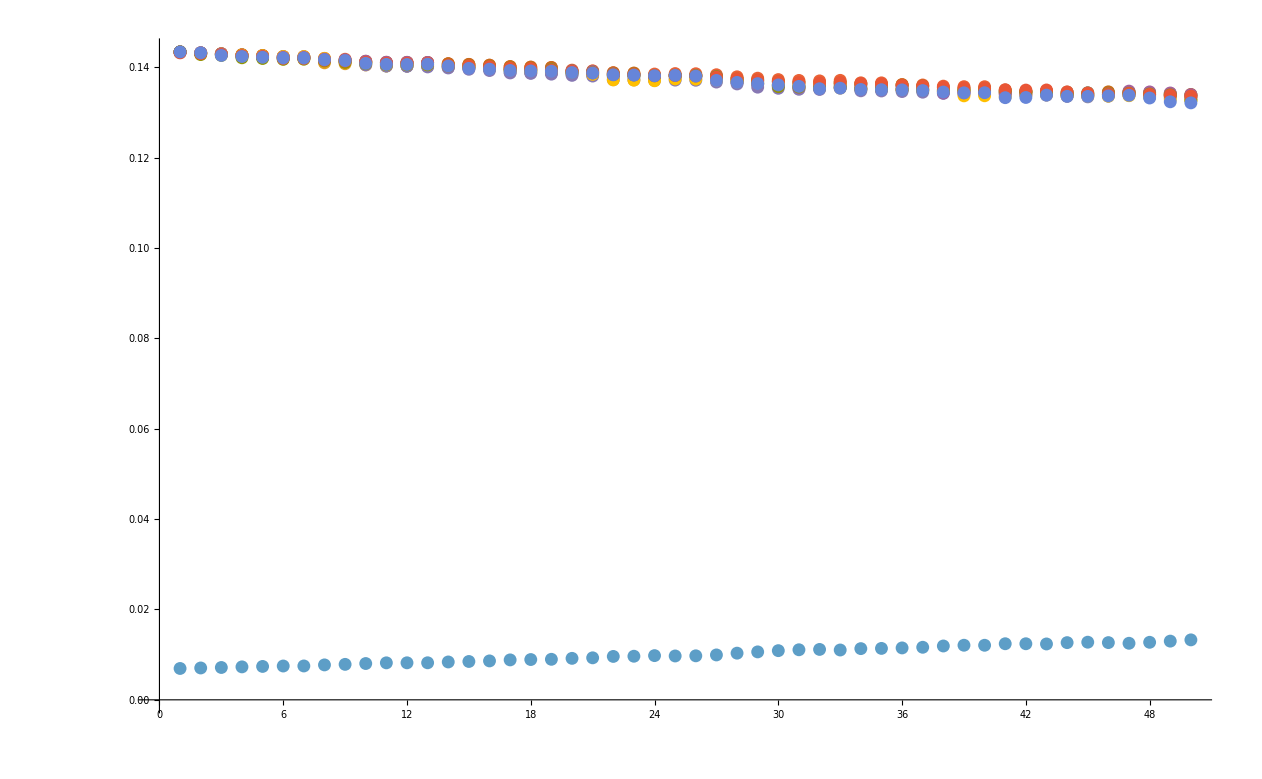

```mathematica
ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic,PlotRange->All]
```

```mathematica
Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

-Graphics-

## 12 Qubits on a lattice

## Unitary translationally invariant (same everywhere at every time step)

### Two qubit pocket

### Four qubit pocket

## Random unitary in each pocket

### Two qubit pocket

### Four qubit pocket

## 16-Qubit gas model with one qubit temperature variation

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5],Subscript[𝒬, 6],Subscript[𝒬, 7],Subscript[𝒬, 8],Subscript[𝒬, 9],Subscript[𝒬, 10],Subscript[𝒬, 11],Subscript[𝒬, 12],Subscript[𝒬, 13],Subscript[𝒬, 14],Subscript[𝒬, 15],Subscript[𝒬, 16]};
vals = RandomSample[Table[i,{i,16}]];
Association[Table[items[[i]]-> vals[[i]],{i,16}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,Hi3,Hi4, interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,4];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^12]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction,IdentityMatrix[2^8]];
Hi3= KroneckerProduct[IdentityMatrix[2^8],SubsysInteraction,IdentityMatrix[2^4]];
Hi4= KroneckerProduct[IdentityMatrix[2^12],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2+Hi3+Hi4) .1]]
]
ρi = NThermalQBit[{.2,.2,.2,.2,.2,.2,.2,.2,.4,.2,.2,.2,.2,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO = RandomOrder[];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,150}];
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]


ChangeinExtractablework//MatrixPlot



ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]


Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

## 16-Qubit gas model with multiple qubit temperature variation

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomOrder[]:=Module[{items,vals},
items = {Subscript[𝒬, 1],Subscript[𝒬, 2],Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5],Subscript[𝒬, 6],Subscript[𝒬, 7],Subscript[𝒬, 8],Subscript[𝒬, 9],Subscript[𝒬, 10],Subscript[𝒬, 11],Subscript[𝒬, 12],Subscript[𝒬, 13],Subscript[𝒬, 14],Subscript[𝒬, 15],Subscript[𝒬, 16]};
vals = RandomSample[Table[i,{i,16}]];
Association[Table[items[[i]]-> vals[[i]],{i,16}]]
]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,Hi3,Hi4, interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,4];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^12]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction,IdentityMatrix[2^8]];
Hi3= KroneckerProduct[IdentityMatrix[2^8],SubsysInteraction,IdentityMatrix[2^4]];
Hi4= KroneckerProduct[IdentityMatrix[2^12],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2+Hi3+Hi4) .1]]
]
ρi = NThermalQBit[{.2,.4,.2,.2,.2,.2,.2,.2,.4,.2,.2,.2,.2,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO = RandomOrder[];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,150}];
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]


ChangeinExtractablework//MatrixPlot



ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]


Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

## 16-Qubit gas model with two qubit nearest neighbour interaction (one temp variation)

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,Hi5,Hi6,Hi7,Hi8,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,Hi3,Hi4,Hi5,Hi6,Hi7,Hi8,interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,2];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^14]];
Hi2= KroneckerProduct[IdentityMatrix[2^2],SubsysInteraction,IdentityMatrix[2^12]];
Hi3=KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction,IdentityMatrix[2^10]];
Hi4=KroneckerProduct[IdentityMatrix[2^6],SubsysInteraction,IdentityMatrix[2^8]];
Hi5 = KroneckerProduct[IdentityMatrix[2^8],SubsysInteraction,IdentityMatrix[2^6]];
Hi6= KroneckerProduct[IdentityMatrix[2^10],SubsysInteraction,IdentityMatrix[2^4]];
Hi7=KroneckerProduct[IdentityMatrix[2^12],SubsysInteraction,IdentityMatrix[2^2]];
Hi8=KroneckerProduct[IdentityMatrix[2^14],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2+Hi3+Hi4+Hi5+Hi6+Hi7+Hi8) .1]]
]
PossibleOrders = {
<|Subscript[𝒬, 1]->1,Subscript[𝒬, 2]->2,Subscript[𝒬, 3]->3,Subscript[𝒬, 4]->4,Subscript[𝒬, 5]->5,Subscript[𝒬, 6]->6,Subscript[𝒬, 7]->7,Subscript[𝒬, 8]->8,Subscript[𝒬, 9]->9,Subscript[𝒬, 10]->10,Subscript[𝒬, 11]->11,Subscript[𝒬, 12]->12,Subscript[𝒬, 13]->13,Subscript[𝒬, 14]->14,Subscript[𝒬, 15]->15,Subscript[𝒬, 16]->16|>,
<|Subscript[𝒬, 1]-> 16,Subscript[𝒬, 2]-> 1,Subscript[𝒬, 3]-> 2,Subscript[𝒬, 4]-> 3,Subscript[𝒬, 5]-> 4,Subscript[𝒬, 6]-> 5,Subscript[𝒬, 7]-> 6,Subscript[𝒬, 8]-> 7,Subscript[𝒬, 9]->8,Subscript[𝒬, 10]->9,Subscript[𝒬, 11]->10,Subscript[𝒬, 12]->11,Subscript[𝒬, 13]->12,Subscript[𝒬, 14]->13,Subscript[𝒬, 15]->14,Subscript[𝒬, 16]->15|>
};
ρi = NThermalQBit[{.2,.2,.2,.2,.2,.2,.2,.2,.4,.2,.2,.2,.2,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO = RandomOrder[];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,150}];
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]


ChangeinExtractablework//MatrixPlot



ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]


Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

## 16-Qubit gas model with two qubit nearest neighbour interaction (multiple temperature variation)

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,Hi5,Hi6,Hi7,Hi8,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,Hi3,Hi4,Hi5,Hi6,Hi7,Hi8,interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,2];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^14]];
Hi2= KroneckerProduct[IdentityMatrix[2^2],SubsysInteraction,IdentityMatrix[2^12]];
Hi3=KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction,IdentityMatrix[2^10]];
Hi4=KroneckerProduct[IdentityMatrix[2^6],SubsysInteraction,IdentityMatrix[2^8]];
Hi5 = KroneckerProduct[IdentityMatrix[2^8],SubsysInteraction,IdentityMatrix[2^6]];
Hi6= KroneckerProduct[IdentityMatrix[2^10],SubsysInteraction,IdentityMatrix[2^4]];
Hi7=KroneckerProduct[IdentityMatrix[2^12],SubsysInteraction,IdentityMatrix[2^2]];
Hi8=KroneckerProduct[IdentityMatrix[2^14],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2+Hi3+Hi4+Hi5+Hi6+Hi7+Hi8) .1]]
]
PossibleOrders = {
<|Subscript[𝒬, 1]->1,Subscript[𝒬, 2]->2,Subscript[𝒬, 3]->3,Subscript[𝒬, 4]->4,Subscript[𝒬, 5]->5,Subscript[𝒬, 6]->6,Subscript[𝒬, 7]->7,Subscript[𝒬, 8]->8,Subscript[𝒬, 9]->9,Subscript[𝒬, 10]->10,Subscript[𝒬, 11]->11,Subscript[𝒬, 12]->12,Subscript[𝒬, 13]->13,Subscript[𝒬, 14]->14,Subscript[𝒬, 15]->15,Subscript[𝒬, 16]->16|>,
<|Subscript[𝒬, 1]-> 16,Subscript[𝒬, 2]-> 1,Subscript[𝒬, 3]-> 2,Subscript[𝒬, 4]-> 3,Subscript[𝒬, 5]-> 4,Subscript[𝒬, 6]-> 5,Subscript[𝒬, 7]-> 6,Subscript[𝒬, 8]-> 7,Subscript[𝒬, 9]->8,Subscript[𝒬, 10]->9,Subscript[𝒬, 11]->10,Subscript[𝒬, 12]->11,Subscript[𝒬, 13]->12,Subscript[𝒬, 14]->13,Subscript[𝒬, 15]->14,Subscript[𝒬, 16]->15|>
};
ρi = NThermalQBit[{.2,.2,.2,.2,.4,.2,.2,.2,.4,.2,.2,.2,.2,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO = RandomOrder[];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,150}];
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]


ChangeinExtractablework//MatrixPlot



ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]


Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

## 16-Qubits on a lattice

```mathematica
Clear[SubsysInteraction,Hi1,Hi2,Hi3,Hi4,Hi5,Hi6,Hi7,Hi8,interactionUnitary,RandomUnitary,PossibleOrders,ρi,DMS,AmbientPops,AmbientTemps,ExtractableWorkOverTime,ChangeinExtractablework]
RandomUnitary:=Module[{SubsysInteraction,Hi1,Hi2,Hi3,Hi4,Hi5,Hi6,Hi7,Hi8,interactionUnitary},
SubsysInteraction = RandomHamiltonian[1,2];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^14]];
Hi2= KroneckerProduct[IdentityMatrix[2^2],SubsysInteraction,IdentityMatrix[2^12]];
Hi3=KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction,IdentityMatrix[2^10]];
Hi4=KroneckerProduct[IdentityMatrix[2^6],SubsysInteraction,IdentityMatrix[2^8]];
Hi5 = KroneckerProduct[IdentityMatrix[2^8],SubsysInteraction,IdentityMatrix[2^6]];
Hi6= KroneckerProduct[IdentityMatrix[2^10],SubsysInteraction,IdentityMatrix[2^4]];
Hi7=KroneckerProduct[IdentityMatrix[2^12],SubsysInteraction,IdentityMatrix[2^2]];
Hi8=KroneckerProduct[IdentityMatrix[2^14],SubsysInteraction];
interactionUnitary =  SparseArray[MatrixExp[I (Hi1+Hi2+Hi3+Hi4+Hi5+Hi6+Hi7+Hi8) .1]]
]
PossibleOrders = {
<|Subscript[𝒬, 1]->1,Subscript[𝒬, 2]->2,Subscript[𝒬, 3]->3,Subscript[𝒬, 4]->4,Subscript[𝒬, 5]->5,Subscript[𝒬, 6]->6,Subscript[𝒬, 7]->7,Subscript[𝒬, 8]->8,Subscript[𝒬, 9]->9,Subscript[𝒬, 10]->10,Subscript[𝒬, 11]->11,Subscript[𝒬, 12]->12,Subscript[𝒬, 13]->13,Subscript[𝒬, 14]->14,Subscript[𝒬, 15]->15,Subscript[𝒬, 16]->16|>,
<|Subscript[𝒬, 1]-> 16,Subscript[𝒬, 2]-> 1,Subscript[𝒬, 3]-> 2,Subscript[𝒬, 4]-> 3,Subscript[𝒬, 5]-> 4,Subscript[𝒬, 6]-> 5,Subscript[𝒬, 7]-> 6,Subscript[𝒬, 8]-> 7,Subscript[𝒬, 9]->8,Subscript[𝒬, 10]->9,Subscript[𝒬, 11]->10,Subscript[𝒬, 12]->11,Subscript[𝒬, 13]->12,Subscript[𝒬, 14]->13,Subscript[𝒬, 15]->14,Subscript[𝒬, 16]->15|>
};
ρi = NThermalQBit[{.2,.2,.2,.2,.2,.2,.2,.2,.4,.2,.2,.2,.2,.2,.2,.2}];
ρ = ρi;
baseOrder = ρ[qbitIDs];
interactionUnitary = RandomUnitary;
DMS = Table[
RO = RandomOrder[];
Ui =MakeDM[interactionUnitary,RO];
ρ = Ui.ReOrder[ρ,RO].Transpose[Ui];
Round[ReOrder[ρ,baseOrder],10^-15],{i,150}];
AmbientTemps = Table[
Association[Table[
qbit-> T[PTR[Ρ,{qbit}]],{qbit,Keys[Ρ[qbitIDs]]}]]
,
{Ρ,DMS}];
AmbientPops= Table[
Association[Table[
qbit->PopFromTemp[Temps[qbit][[2]]],{qbit,Keys[Temps]}]],
{Temps,AmbientTemps}];
ExtractableWorkOverTime= N[Module[{Ρ},
Table[
Ρ = DMS[[t]];
Table[
AmbientTemps[[t]][qbit] D[PTR[Ρ,DeleteCases[Keys[Ρ[qbitIDs]],qbit]]||ThermalQBit[AmbientPops[[t]][qbit]]
],
{qbit,Keys[Ρ[qbitIDs]]}],
{t,Length[DMS]}]
]];
ChangeinExtractablework=Table[ExtractableWorkOverTime[[i+1]]-ExtractableWorkOverTime[[i]],{i,Length[ExtractableWorkOverTime]}];
ListPlot[Transpose[ChangeinExtractablework],AxesLabel->Automatic,PlotRange->All]


ChangeinExtractablework//MatrixPlot



ListPlot[Transpose[ExtractableWorkOverTime],AxesLabel->Automatic]


Table[
Table[
N[Temp[PartialTrace[img,DeleteCases[Keys[img[qbitIDs]],Q]]],5],{Q,Keys[img[qbitIDs]]}],{img,DMS}]//MatrixPlot
```

## Unitary translationally invariant (same everywhere at every time step)

### Two qubit pocket

### Four qubit pocket

```mathematica
LatticePoints = {{q1,1,2,5,6},{q2,2,3,6,7},{q3,3,4,7,8},{q4,4,1,8,5},{q5,5,6,9,10},{q6,6,7,10,11},{q7,7,8,11,12},{q8,8,5,12,9},{q9,9,10,13,14},{q10,10,11,14,15},{q11,11,12,15,16},{q12,12,9,16,13},{q13,13,14,1,2},{q14,14,15,2,3},{q15,15,15,3,4},{q16,16,13,4,1}};
x = RandomChoice[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}]
Print[x]
val =Mod[x,4]
```

4

4

0

```mathematica
Clear[Points,Sets]
```

```mathematica
x = RandomChoice[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}];
Clear[Points,Sets]
For[Points = 1;Sets = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16};Print[x],Points<4,Points++,If[Mod[x,4]==0,Sets=DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[Sets,Mod[x,16]],Mod[x-1,16]],Mod[x-3,16]],Mod[x-4,16]],Mod[x+4,16]],Mod[x+3,16]],Mod[x-5,16]],Mod[x-7,16]],Mod[x+1,16]];p2= RandomChoice[Sets];Print[p2],Null];If[Mod[x,4]==1,Sets= DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[Sets,Mod[x,16]],Mod[x-1,16]],Mod[x-3,16]],Mod[x-4,16]],Mod[x+4,16]],Mod[x+3,16]],Mod[x+5,16]],Mod[x+7,16]],Mod[x+1,16]];p2= RandomChoice[Sets];Print[p2],Null];If[Mod[x,4]==2||3,Sets=DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[Sets,Mod[x,16]],Mod[x-1,16]],Mod[x-3,16]],Mod[x-4,16]],Mod[x+4,16]],Mod[x+3,16]],Mod[x-5,16]],Mod[x+5,16]],Mod[x+1,16]];p2= RandomChoice[Sets];Print[p2],Null];x=p2;Clear[p2]]
```

6

4

14

16

```mathematica
If[val==0,p2= RandomChoice[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Mod[x,16]],Mod[x-1,16]],Mod[x-3,16]],Mod[x-4,16]],Mod[x+4,16]],Mod[x+3,16]],Mod[x-5,16]],Mod[x-7,16]],Mod[x+1,16]]];Print[p2],Null]
Clear[p2]
If[Mod[x,4]==1,p2= RandomChoice[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[DeleteCases[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},Mod[x,16]],Mod[x-1,16]],Mod[x-3,16]],Mod[x-4,16]],Mod[x+4,16]],Mod[x+3,16]],Mod[x+5,16]],Mod[x+7,16]],Mod[x+1,16]]];Print[p2],Null]
Clear[p2]
```

8

8

0

2

## Random unitary in each pocket

### Two qubit pocket

### Four qubit pocket